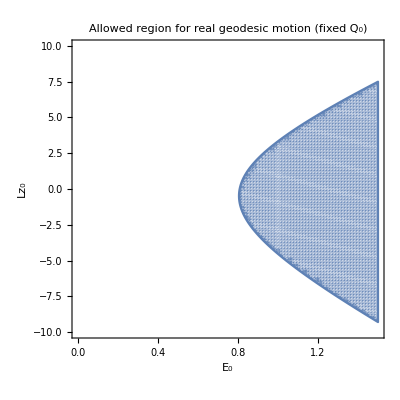

```mathematica
ρ=r^2+a^2 Cos[θ]^2; 
Δ=r^2-2 m r+a^2;

(*Usual Boyer-Lindquist*)
metric=-{{-ρ/Δ,0,0,0},{0,-ρ,0,0},{0,0,-(((r^2+a^2)^2-Δ a Sin[θ]^2)/ρ) Sin[θ]^2,(a Sin[θ]^2( r^2 +a^2-Δ))/ρ},{0,0,(a Sin[θ]^2( r^2 +a^2-Δ))/ρ,(Δ-a^2 Sin[θ]^2)/ρ}};

Delta=r0^2-2 m0 r0+a0^2;
rho2=r0^2+a0^2 Cos[th0]^2;
sinth2=Sin[th0]^2;
costh2=Cos[th0]^2;
csc2=1/sinth2;

{grr,gθθ,gϕϕ,gtϕ,gtt}={metric[[1,1]],metric[[2,2]],metric[[3,3]],metric[[3,4]],metric[[4,4]]} /. {r->r0,θ->th0,m->m0,a->a0};
det=gtϕ^2-gtt*gϕϕ;

dt=(gϕϕ*E0+gtϕ*Lz0)/det;
dph=(-gtϕ*E0-gtt*Lz0)/det;
dth2= Q0-costh2(a0^2(1-E0^2)+(Lz0^2 *csc2));
dth=Sqrt[dth2/gθθ];
dr2=-1-gtt*dt^2-2*gtϕ*dt*dph-gϕϕ*dph^2-gθθ*dth^2;
dr=-Sqrt[dr2/grr];

dth=pθ/rho2;
dr=(Delta/rho2)pr;

(*Fixed values*)
a0=0.9;
m0=1;
r0=5;
th0=Pi/3;
Q0=2;

(*Carter radial potential R(r)*)
Rr[E0_,Lz0_]:=((r0^2+a0^2)*E0-a0*Lz0)^2-Delta*(Q0+(Lz0-a0*E0)^2+r0^2);

(*Condition:R(r0)≥0 for real\dot{r}*)
RegionPlot[Rr[E0,Lz0]>=0,{E0,0,1.5},{Lz0,-10,10},PlotPoints->100,FrameLabel->{"E₀","Lz₀"},PlotLabel->"Allowed region for real geodesic motion (fixed Q₀)",Frame->True]
```

-Graphics3D-

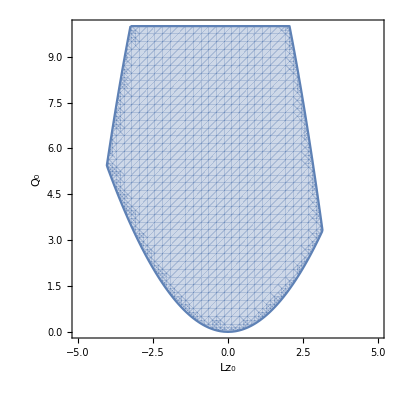

```mathematica
Rr2[E0_,Lz0_,Q0_]:=((r0^2+a0^2)*E0-a0*Lz0)^2-Delta*(Q0+(Lz0-a0*E0)^2+r0^2);
thetaIneq[E0_,Lz0_,Q0_]:=Q0>Cos[th0]^2 (a0^2 (1-E0^2)+Lz0^2/Sin[th0]^2);
RegionPlot3D[Rr2[E0,Lz0,Q0]>=0&&thetaIneq[E0,Lz0,Q0],{E0,0.5,1.5},{Lz0,-5,5},{Q0,0,10},PlotPoints->40,AxesLabel->{"E₀","Lz₀","Q₀"},PlotLabel->"Timelike geodesics: Real \!\(\*SuperscriptBox[\(r\), \('\)]\), \!\(\*SuperscriptBox[\(θ\), \('\)]\)"]
RegionPlot[Rr2[1,Lz0,Q0]>=0&&thetaIneq[1,Lz0,Q0],{Lz0,-5,5},{Q0,0,10},PlotPoints->40,FrameLabel->{"Lz₀","Q₀"}]
```

```mathematica
isValidInitialCondition[E0_?NumericQ,Lz0_?NumericQ,Q0_?NumericQ]:=Module[{Rval,thetaOk},Rval=Rr[E0,Lz0,Q0];
thetaOk=thetaIneq[E0,Lz0,Q0];
Rval>=0&&thetaOk];
isValidInitialCondition[1,2.0,2.5]
(*Output:True or False*)
```

True